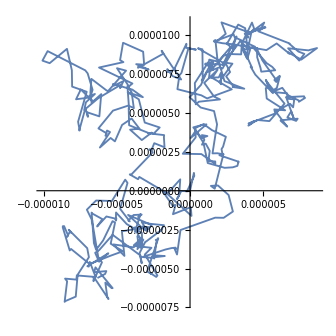

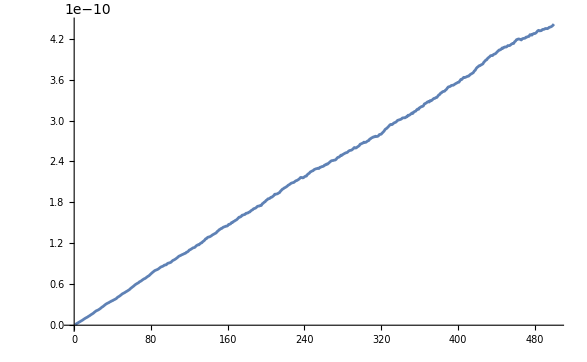

1.41845×10^-23

```mathematica
dispers=3; (*Дисперсия*)
mat=1; (*Математическое ожидание*)
b=0.3*10^-6; (*Коэффицент масштаба*)
t=500; (*Время замера движения молекулы*)
NN=500; (*количесвто итераций для траектории*)
numRuns = 1000; (*Количество итераций для усреднения квадрата смещения*)
m=Table[0,{NN}];
deltT=t/NN;(*Коэффицент масштаба для времени*)

x1 = 0;
y1 = 0;
xyList={{0,0}};
For[i=1,i<=NN,i++,
xi=RandomVariate[NormalDistribution[mat,dispers]];
theta=RandomReal[{0,2 Pi}];
x1=x1+b*xi*deltT*Cos[theta];
y1=y1+b*xi*deltT*Sin[theta];
xyList=Append[xyList,{x1,y1}];]

ListLinePlot[xyList,PlotStyle->Thickness[0.004],AspectRatio->1]

(*ВСЁ ДЛЯ ВТОРОГО ГРАФИКА*)
For[run=1,run<=numRuns,run++,
x=0;
y=0;

For[i=1,i<=NN,i++,
xi=RandomVariate[NormalDistribution[mat,dispers]];
theta=RandomReal[{0,2 Pi}];
x+=b*xi*deltT*Cos[theta];
y+=b*xi*deltT*Sin[theta];
d=x^2+y^2;(*Квадрат расстояние от отначала координат, т.е. 
смещение*)
m[[i]]+=d;]]

m=m/numRuns; (*Средняя велечина смещения*)
res=Table[{i*deltT,m[[i]]},{i,1,NN}]; (*1 - время, 2 - квадрат среднего смещения*)
ListLinePlot[res]
Sum[(3*Pi*10^-9*0.5)/300*res[[i,2]]/res[[i,1]],{i,1,NN}]/NN  (*Формула Эйнштейна*)
```